```mathematica
(Subsets[#,{3}]&/@(Table[Prime[n],{n,2,10}]//Subsets[#,{4}]&))/.{x__}/;Length[{x}]==3:>Boole[PrimeQ[Total[{x}]]]//Length
```

126

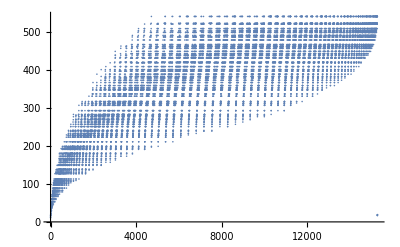

```mathematica
(Table[IntegerPartitions[Prime[n],{3}],{n,2,100}]/.{x_,y_,z_}/;Not@g[{x,y,z}]->Nothing//Cases[#,{_,_,_},Infinity]&//Sort)/.{x__Integer}:> Total[{x}]//Flatten//ListPlot
```

```mathematica
if[i_ in  l_ ,c1_,c2_ ]:=
If[MemberQ[l,i,Infinity],c1 ,c2 ]
```

```mathematica
m={ 1,2,{3,4},5,6}
```

```mathematica
{1,2,{{3},4},5,6}
```

{1,2,{{3},4},5,6}

```mathematica
if[9 in m, Print["y"],Print["n"] ]
```

n

```mathematica
if[3 in m,Print["y"],Print["n"]]
```

y

```mathematica
SetAttributes[if,HoldFirst]
```

```mathematica
Attributes[if]
```

{HoldAll}

```mathematica
Clear@ if
```

```mathematica
?if
```

Global`if

Attributes[if]={HoldAll}
 
if[i_ in l_List,c1_,c2_]:=If[MemberQ[Flatten[l],i],c1,c2]
 
if[i_ in l_,c1_,c2_]:=If[MemberQ[l,i,∞],c1,c2]

```mathematica
Scan
```

def moveTower(n, source,  dest, temp):
  if n == 1:
    print("Move disk from", source, "to", dest+" . ")
  else:
    moveTower(n-1, source, temp, dest)
    moveTower(1, source, dest, temp)
    moveTower(n-1, temp, dest, source)
    
def hanoi(n):
   moveTower(n, "A", "C", "B")    

hanoi(3)

```mathematica
move [n_,s_,d_,t_]:=
If[n==1,
Print["move disk from ",s," to  ",d,"."],
move[n-1,s,t,d];
move[1,s,d,t];
move[n-1,t,d,s]]
h[n_]:=
move[n,"A","C","B"]
```

```mathematica
h[5]
```

move disk from A to  C.

move disk from A to  B.

move disk from C to  B.

move disk from A to  C.

move disk from B to  A.

move disk from B to  C.

move disk from A to  C.

move disk from A to  B.

move disk from C to  B.

move disk from C to  A.

move disk from B to  A.

move disk from C to  B.

move disk from A to  C.

move disk from A to  B.

move disk from C to  B.

move disk from A to  C.

move disk from B to  A.

move disk from B to  C.

move disk from A to  C.

move disk from B to  A.

move disk from C to  B.

move disk from C to  A.

move disk from B to  A.

move disk from B to  C.

move disk from A to  C.

move disk from A to  B.

move disk from C to  B.

move disk from A to  C.

move disk from B to  A.

move disk from B to  C.

move disk from A to  C.

import socket
x= socket.getservbyname("ftp")
print (x)

21

```mathematica
f[]
```